## Sign error in Linkwitz-Riley second order crossover filters

We plot the transfer function of the second order Linkwitz-Riley lowpass filter with cutoff at 0.5 radians:

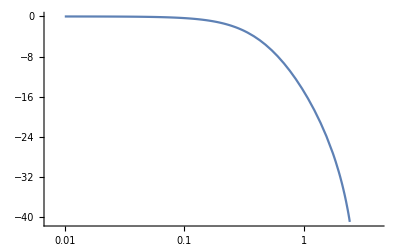

```mathematica
(* some helper functions *)
γ[fc_]:=Tan[fc/2] (* fc in radians*)
zz[ω_]:=ⅇ^(ⅈ ω) (* convert ω in radians to complex number z *)
linearToDb[linear_]:=20Log10[linear]

(* a0, a1, a2. Note a0 will be normalised to 1 so all others are divided by a0 *)
a0lp[γ_]:=γ^2+2 γ+1
a1lp[γ_]:=2 (γ^2-1)/a0lp[γ]
a2lp[γ_]:=(γ^2-2 γ+1)/a0lp[γ]

(* b0, b1, b2 *)
b0lp[γ_]:=γ^2/a0lp[γ]
b1lp[γ_]:=2 b0lp[γ]
b2lp[γ_]:=b0lp[γ]
         
(* lowpass transfer function *)
lwLp[z_,fc_]:=(b0lp[γ[fc]] + b1lp[γ[fc]]z^(-1) + b2lp[γ[fc]]z^(-2))/(1 + a1lp[γ[fc]]z^(-1) + a2lp[γ[fc]]z^(-2))

LogLinearPlot[linearToDb[Abs[lwLp[zz[ω],0.5]]],{ω,0.01,π}]
```

We plot the highpass transfer function:

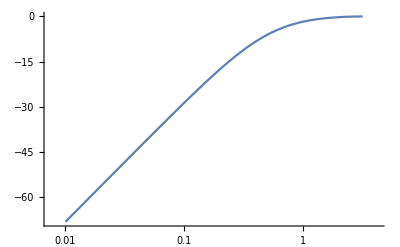

```mathematica
(* a0, a1, a2. Note a0 will be normalised to 1 so all others are divided by a0 *)
a0hp[γ_]:=γ^2+2 γ+1
a1hp[γ_]:=2 (γ^2-1)/a0hp[γ]
a2hp[γ_]:=(γ^2-2 γ+1)/a0hp[γ]
 
(* b0, b1, b2 *)
b0hp[γ_]:=1/a0hp[γ]
b1hp[γ_]:=-2/a0hp[γ]
b2hp[γ_]:=1/a0hp[γ]
    
lwHp[z_,fc_]:=(b0hp[γ[fc]] + b1hp[γ[fc]]z^(-1) + b2hp[γ[fc]]z^(-2))/(1 + a1hp[γ[fc]]z^(-1) + a2hp[γ[fc]]z^(-2))

LogLinearPlot[linearToDb[Abs[lwHp[zz[ω],0.5]]],{ω,0.01,π}]
```

## Summing the lowpass and highpass transfer functions back together

Sum of lowpass and highpass transfer functions. This looks wrong.

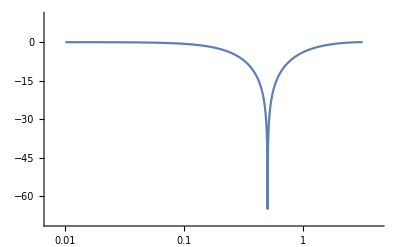

```mathematica
LogLinearPlot[linearToDb[Abs[lwHp[zz[ω],0.5]+lwLp[zz[ω],0.5]]],{ω,0.01,π}, PlotRange->{-70, 10}]
```

Difference of lowpass and highpass transfer functions. This looks correct and indicates that one of the two filters should have its b coefficients negated. I think we should negate the coefficients on the highpass filter.

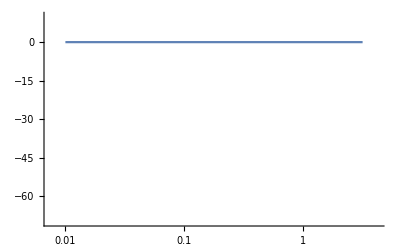

```mathematica
LogLinearPlot[linearToDb[Abs[lwLp[zz[ω],0.5]-lwHp[zz[ω],0.5]]],{ω,0.01,π}, PlotRange->{-70, 10}]
```

## Fourth order case

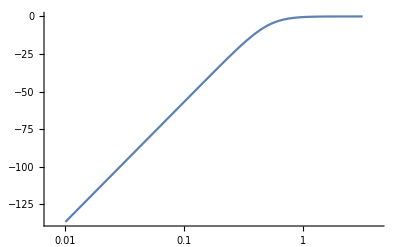

```mathematica
(* fourth order linkwitz-riley highpass *)

(* second order butterworth coefficients *)
a0bwhp[γ_] = γ^2 + Sqrt[2] γ + 1;
a1bwhp[γ_]=2(γ^2-1)/a0bwhp[γ];
a2bwhp[γ_]=(γ^2-Sqrt[2] γ+1.0)/a0bwhp[γ];

b0bwhp[γ_]=1.0/a0bwhp[γ];
b1bwhp[γ_]=-2.0/a0bwhp[γ];
b2bwhp[γ_]= 1.0/a0bwhp[γ];

(* butterworth highpass transfer function *)
bwHp[z_,fc_]:=(b0bwhp[γ[fc]] + b1bwhp[γ[fc]]z^(-1) + b2bwhp[γ[fc]]z^(-2))/(1 + a1bwhp[γ[fc]]z^(-1) + a2bwhp[γ[fc]]z^(-2))

(* fourth order linkwitz-riley tf *)
lwHp4[z_,fc_]:=bwHp[z,fc]^2

LogLinearPlot[linearToDb[Abs[lwHp4[zz[ω],0.5]]],{ω,0.01,π}]
```

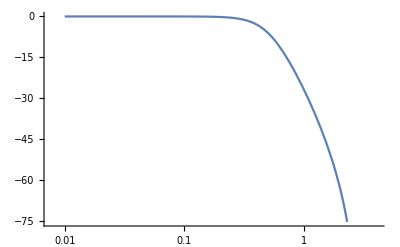

```mathematica
(*
   b0=gamma_sq*one_over_denominator;
   b1=2.0* *b0;
   b2= b0;

   a1=2.0*(gamma_sq-1.0)*one_over_denominator;
   a2=(gamma_sq-sqrt_2_gamma+1.0)*one_over_denominator;
*)

(* fourth order linkwitz-riley lowpass *)

(* second order butterworth coefficients *)
a0bwlp[γ_] = γ^2 + Sqrt[2] γ + 1;
a1bwlp[γ_]=2(γ^2-1)/a0bwlp[γ];
a2bwlp[γ_]=(γ^2-Sqrt[2] γ+1.0)/a0bwlp[γ];

b0bwlp[γ_]=γ^2/a0bwlp[γ];
b1bwlp[γ_]=2 γ^2/a0bwlp[γ];
b2bwlp[γ_]= γ^2/a0bwlp[γ];

(* butterworth highpass transfer function *)
bwLp[z_,fc_]:=(b0bwlp[γ[fc]] + b1bwlp[γ[fc]]z^(-1) + b2bwlp[γ[fc]]z^(-2))/(1 + a1bwlp[γ[fc]]z^(-1) + a2bwlp[γ[fc]]z^(-2))

(* fourth order linkwitz-riley tf *)
lwLp4[z_,fc_]:=bwLp[z,fc]^2

LogLinearPlot[linearToDb[Abs[lwLp4[zz[ω],0.5]]],{ω,0.01,π}]
```

## We plot the sum of the transfer functions of the 4th order L-R highpass and lowpass filters

```mathematica
LogLinearPlot[linearToDb[Abs[lwLp4[zz[ω],0.5]+lwHp4[zz[ω],0.5]]],{ω,0.01,π}, PlotRange->{-70, 10}]
```

-Graphics-

It looks like there is no problem with the sign of the highpass filter in the fourth order L-R crossover

## We plot the sum of butterworth lowpass and highpass TF to see what would happen if we use them as a crossover. We need a 3dB hump at the cutoff to get equal power when the phase of the signal is distorted

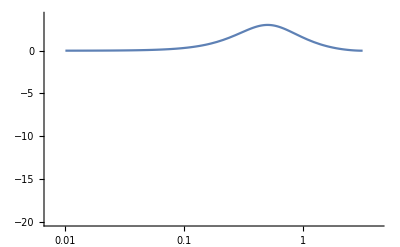

```mathematica
LogLinearPlot[linearToDb[Abs[bwLp[zz[ω],0.5]-bwHp[zz[ω],0.5]]],{ω,0.01,π},PlotRange->{-20,4}]
```